# S2 Example: Spin System

Lecamwasam, R, Iakovleva, T, & Twamley, J (2024). Quantum metrology with linear Lie algebra parameterizations Phys. Rev. Res., 6, 043137 arxiv:2311.12446.

## Lie algebra

```mathematica
Commutator[OverHat[σx],OverHat[σy],2ⅈ OverHat[σz]];
Commutator[OverHat[σy],OverHat[σz],2ⅈ OverHat[σx]];
Commutator[OverHat[σz],OverHat[σx],2ⅈ OverHat[σy]];
algebra={OverHat[σx],OverHat[σy],OverHat[σz]};
```

### Commutation table

```mathematica
AlgCommTable[algebra]
```

| OverHat[σx] | OverHat[σy] | OverHat[σz]
OverHat[σx] | 0 | 2 ⅈ OverHat[σz] | -2 ⅈ OverHat[σy]
OverHat[σy] | -2 ⅈ OverHat[σz] | 0 | 2 ⅈ OverHat[σx]
OverHat[σz] | 2 ⅈ OverHat[σy] | -2 ⅈ OverHat[σx] | 0

```mathematica
AlgCommTable[algebra,Xj->True]
```

| X_1 | X_2 | X_3
X_1 | 0 | 2 ⅈ X_3 | -2 ⅈ X_2
X_2 | -2 ⅈ X_3 | 0 | 2 ⅈ X_1
X_3 | 2 ⅈ X_2 | -2 ⅈ X_1 | 0

```mathematica
adjRep=AdjointRep[algebra];
Print["Adjoint representation:"]
Print[Subscript[ad, #[[1]]]," = ",MatrixForm@#[[2]]]&/@Transpose@{algebra,adjRep};
```

Adjoint representation:

ad_OverHat[σx] = (0 | 0 | 0
0 | 0 | -2 ⅈ
0 | 2 ⅈ | 0)

ad_OverHat[σy] = (0 | 0 | 2 ⅈ
0 | 0 | 0
-2 ⅈ | 0 | 0)

ad_OverHat[σz] = (0 | -2 ⅈ | 0
2 ⅈ | 0 | 0
0 | 0 | 0)

## Fernández solution

```mathematica
$Assumptions={0<θ<2π};
hCoeffs={Sin[θ],Cos[θ],0};

Print["Hamilton: ",Ham=Total@Flatten@Thread@{hCoeffs*algebra}];
```

Hamilton: Cos[θ] OverHat[σy]+OverHat[σx] Sin[θ]

```mathematica
MakeLieH[hCoeffs,algebra,algebra]//FullSimplify//MatrixForm
```

(0 | 0 | -2 ⅈ Cos[θ]
0 | 0 | 2 ⅈ Sin[θ]
2 ⅈ Cos[θ] | -2 ⅈ Sin[θ] | 0)

```mathematica
{ut,eom}=MakeLieEOM[hCoeffs,algebra,algebra]//FullSimplify;
sol=Flatten@DSolve[Flatten@eom,Flatten@ut,t]//FullSimplify
```

{u[1,1,t]→Cos[t]^2-Cos[2 θ] Sin[t]^2,u[2,1,t]→Sin[t]^2 Sin[2 θ],u[3,1,t]→-Cos[θ] Sin[2 t],u[1,2,t]→Sin[t]^2 Sin[2 θ],u[2,2,t]→Cos[t]^2+Cos[2 θ] Sin[t]^2,u[3,2,t]→Sin[2 t] Sin[θ],u[1,3,t]→Cos[θ] Sin[2 t],u[2,3,t]→-Sin[2 t] Sin[θ],u[3,3,t]→Cos[2 t]}

```mathematica
σxyzt=Table[Sum[u[j,k,t]algebra[[k]],{k,1,Length@algebra}],{j,1,Length@algebra}]/.sol;
PrintσSol[params_]:=(
Print["H = ",Ham/.params];
(Print[#[[1]],"(t) = ",#[[2]]]&/@Thread[{algebra,σxyzt/.params//FullSimplify}];)
);

PrintσSol[{}]
```

H = Cos[θ] OverHat[σy]+OverHat[σx] Sin[θ]

OverHat[σx](t) = OverHat[σx] (Cos[t]^2-Cos[2 θ] Sin[t]^2)+Cos[θ] OverHat[σz] Sin[2 t]+OverHat[σy] Sin[t]^2 Sin[2 θ]

OverHat[σy](t) = OverHat[σy] (Cos[t]^2+Cos[2 θ] Sin[t]^2)-OverHat[σz] Sin[2 t] Sin[θ]+OverHat[σx] Sin[t]^2 Sin[2 θ]

OverHat[σz](t) = Cos[2 t] OverHat[σz]+Sin[2 t] (-Cos[θ] OverHat[σx]+OverHat[σy] Sin[θ])

```mathematica
PrintσSol[{θ->0}]
```

H = OverHat[σy]

OverHat[σx](t) = Cos[2 t] OverHat[σx]+OverHat[σz] Sin[2 t]

OverHat[σy](t) = OverHat[σy]

OverHat[σz](t) = Cos[2 t] OverHat[σz]-OverHat[σx] Sin[2 t]

```mathematica
PrintσSol[{θ->π/2}]
```

H = OverHat[σx]

OverHat[σx](t) = OverHat[σx]

OverHat[σy](t) = Cos[2 t] OverHat[σy]-OverHat[σz] Sin[2 t]

OverHat[σz](t) = Cos[2 t] OverHat[σz]+OverHat[σy] Sin[2 t]

```mathematica
PrintσSol[{θ->π/4}]
```

H = OverHat[σx]/(√2)+OverHat[σy]/(√2)

OverHat[σx](t) = Cos[t]^2 OverHat[σx]+Sin[t] (√2 Cos[t] OverHat[σz]+OverHat[σy] Sin[t])

OverHat[σy](t) = Cos[t]^2 OverHat[σy]+Sin[t] (-√2 Cos[t] OverHat[σz]+OverHat[σx] Sin[t])

OverHat[σz](t) = Cos[2 t] OverHat[σz]+√2 Cos[t] (-OverHat[σx]+OverHat[σy]) Sin[t]

## Quantum Fisher information

```mathematica
(exparg=-ⅈ s Sum[hCoeffs[[j]]adjRep[[j]],{j,1,Length@algebra}])//MatrixForm
```

(0 | 0 | 2 s Cos[θ]
0 | 0 | -2 s Sin[θ]
-2 s Cos[θ] | 2 s Sin[θ] | 0)

```mathematica
(integrand=MatrixExp[exparg]//FullSimplify)//MatrixForm
```

(Cos[s]^2-Cos[2 θ] Sin[s]^2 | Sin[s]^2 Sin[2 θ] | Cos[θ] Sin[2 s]
Sin[s]^2 Sin[2 θ] | Cos[s]^2+Cos[2 θ] Sin[s]^2 | -Sin[2 s] Sin[θ]
-Cos[θ] Sin[2 s] | Sin[2 s] Sin[θ] | Cos[2 s])

```mathematica
(eInt=Integrate[integrand,{s,0,t}]//FullSimplify)//MatrixForm
```

(1/4 (2 t+Sin[2 t]+Cos[2 θ] (-2 t+Sin[2 t])) | Cos[θ] (t-Cos[t] Sin[t]) Sin[θ] | Cos[θ] Sin[t]^2
Cos[θ] (t-Cos[t] Sin[t]) Sin[θ] | t Cos[θ]^2+Cos[t] Sin[t] Sin[θ]^2 | -Sin[t]^2 Sin[θ]
-Cos[θ] Sin[t]^2 | Sin[t]^2 Sin[θ] | Cos[t] Sin[t])

```mathematica
𝒱=Sum[D[hCoeffs[[j]],θ]eInt.Table[KroneckerDelta[k,j],{k,1,Length@algebra}],{j,1,Length@algebra}]//FullSimplify
Print["𝒱 = ",Sum[𝒱[[j]]algebra[[j]],{j,1,Length@algebra}]]
```

{Cos[t] Cos[θ] Sin[t],-Cos[t] Sin[t] Sin[θ],-Sin[t]^2}

𝒱 = Cos[t] Cos[θ] OverHat[σx] Sin[t]-OverHat[σz] Sin[t]^2-Cos[t] OverHat[σy] Sin[t] Sin[θ]

### Evaluating Fisher information

```mathematica
ψ0={Cos[ϕ],Sin[ϕ]};
ρ0=KroneckerProduct[ψ0,ψ0];
```

```mathematica
sx=({{0, 1}, {1, 0}});
sy=({{0, -ⅈ}, {ⅈ, 0}});
sz=({{1, 0}, {0, -1}});
sp=({{0, 1}, {0, 0}});
sm=({{0, 0}, {1, 0}});

algebraXYZ={sx,sy,sz};
algebraPM={sz,sp,sm};
```

```mathematica
covar[j_,k_,algebra_,ρ_]:=With[
{
Xj=algebra[[j]],
Xk=algebra[[k]]
},
1/2 Tr[(Xj.Xk+Xk.Xj).ρ]-Tr[Xj.ρ]Tr[Xk.ρ]
]
var[j_,algebra_,ρ_]:=covar[j,j,algebra,ρ]

varV[vjList_,algebra_,ρ_]:=Sum[vjList[[j]]^2 var[j,algebra,ρ],{j,1,Length@algebra}]+2Sum[vjList[[j]]vjList[[k]]covar[j,k,algebra,ρ],{j,1,Length@algebra},{k,j+1,Length@algebra}]
```

```mathematica
vListXYZ={Sin[t]Cos[t]Cos[θ],-Sin[t]Cos[t]Sin[θ],-Sin[t]Sin[t]};
qfiXYZ=varV[vListXYZ,algebraXYZ,ρ0]//FullSimplify
```

1/2 Sin[t]^2 (2 Cos[t]^2 (Cos[θ]^2 Cos[2 ϕ]^2+Sin[θ]^2)+2 Sin[t]^2 Sin[2 ϕ]^2+Cos[θ] Sin[2 t] Sin[4 ϕ])

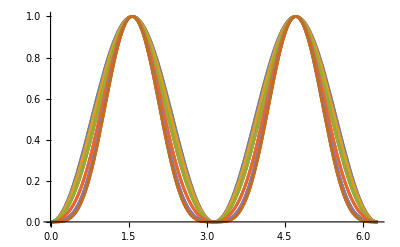

```mathematica
data=Table[qfiXYZ/.{θ->Θ,ϕ->π/4},{Θ,0,2π,π/10.}];
Plot[data,{t,0,2π}]
```

## Wei Norman solution

### Pauli operator solution

```mathematica
weiCoeffs=Table[a[j,t]->-ⅈ hCoeffs[[j]],{j,1,3}];
ut=Table[u[j,t],{j,1,3,1}];
wnEOM=WeiNormanEOM[algebra]/.weiCoeffs/.Equal[a_,b_]:>Equal[a,FullSimplify@b]
```

{u^(0,1)[1,t]==ⅈ (-Cosh[2 u[1,t]]^2 Sin[θ]+Sinh[2 u[1,t]] (Sin[θ] Sinh[2 u[1,t]]+Cos[θ] Tanh[2 u[2,t]])),u^(0,1)[2,t]==-ⅈ Cos[θ] Cosh[2 u[1,t]],u^(0,1)[3,t]==-Cos[θ] Sech[2 u[2,t]] Sinh[2 u[1,t]]}

```mathematica
Print/@wnEOM;
```

u^(0,1)[1,t]==ⅈ (-Cosh[2 u[1,t]]^2 Sin[θ]+Sinh[2 u[1,t]] (Sin[θ] Sinh[2 u[1,t]]+Cos[θ] Tanh[2 u[2,t]]))

u^(0,1)[2,t]==-ⅈ Cos[θ] Cosh[2 u[1,t]]

u^(0,1)[3,t]==-Cos[θ] Sech[2 u[2,t]] Sinh[2 u[1,t]]

```mathematica
wnEOMv=wnEOM/.{u[j_,t]:>v[j,t],Derivative[0,1][u][j_,t]:>Derivative[0,1][v][j,t]}
```

{v^(0,1)[1,t]==ⅈ (-Cosh[2 v[1,t]]^2 Sin[θ]+Sinh[2 v[1,t]] (Sin[θ] Sinh[2 v[1,t]]+Cos[θ] Tanh[2 v[2,t]])),v^(0,1)[2,t]==-ⅈ Cos[θ] Cosh[2 v[1,t]],v^(0,1)[3,t]==-Cos[θ] Sech[2 v[2,t]] Sinh[2 v[1,t]]}

```mathematica
wnEOMv/.{v[j_,t]:>ⅈ u[j,t],Derivative[0,1][v][j_,t]:>ⅈ Derivative[0,1][u][j,t]}//FullSimplify
```

{Sin[θ]+Cos[θ] Sin[2 u[1,t]] Tan[2 u[2,t]]+u^(0,1)[1,t]==0,Cos[θ] Cos[2 u[1,t]]+u^(0,1)[2,t]==0,Cos[θ] Sec[2 u[2,t]] Sin[2 u[1,t]]+u^(0,1)[3,t]==0}

```mathematica
(* Can't be solved analytically
wnIC=Table[u[j,0]==0,{j,1,Length@algebra}];
wnSol=Flatten@DSolve[Join[Flatten@wnEOM,wnIC],Flatten@ut,t]//FullSimplify
*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

```mathematica
wnEOMi=wnEOM/.{u[j_,t]:>ⅈ u[j,t],Derivative[0,1][u][j_,t]:>ⅈ Derivative[0,1][u][j,t]}//FullSimplify
```

{Sin[θ]+Cos[θ] Sin[2 u[1,t]] Tan[2 u[2,t]]+u^(0,1)[1,t]==0,Cos[θ] Cos[2 u[1,t]]+u^(0,1)[2,t]==0,Cos[θ] Sec[2 u[2,t]] Sin[2 u[1,t]]+u^(0,1)[3,t]==0}

```mathematica
(* Can't be solved analytically
wnIC=Table[u[j,0]==0,{j,1,Length@algebra}];
wnSoli=Flatten@DSolve[Join[Flatten@wnEOMi,wnIC],Flatten@ut,t]//FullSimplify
*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

$Aborted

### Permuted EOM

```mathematica
permutations={{1,2,3},{3,1,2},{2,3,1}};
algebraList=Table[Permute[algebra,perm],{perm,permutations}]
weiCoeffsList=Table[Table[a[j,t]->-ⅈ Permute[hCoeffs,perm][[j]],{j,1,Length@algebra}],{perm,permutations}]
```

{{OverHat[σx],OverHat[σy],OverHat[σz]},{OverHat[σy],OverHat[σz],OverHat[σx]},{OverHat[σz],OverHat[σx],OverHat[σy]}}

{{a[1,t]→-ⅈ Sin[θ],a[2,t]→-ⅈ Cos[θ],a[3,t]→0},{a[1,t]→-ⅈ Cos[θ],a[2,t]→0,a[3,t]→-ⅈ Sin[θ]},{a[1,t]→0,a[2,t]→-ⅈ Sin[θ],a[3,t]→-ⅈ Cos[θ]}}

```mathematica
wnEOMList=Table[Join[WeiNormanEOM[algebraList[[j]]]/.weiCoeffsList[[j]],wnIC],{j,1,Length@permutations}];
```

```mathematica
wnEOMListi=wnEOMList/.{u[j_,t]:>ⅈ u[j,t],Derivative[0,1][u][j_,t]:>ⅈ Derivative[0,1][u][j,t]}//FullSimplify
```

{{Sin[θ]+Cos[θ] Sin[2 u[1,t]] Tan[2 u[2,t]]+u^(0,1)[1,t]==0,Cos[θ] Cos[2 u[1,t]]+u^(0,1)[2,t]==0,Cos[θ] Sec[2 u[2,t]] Sin[2 u[1,t]]+u^(0,1)[3,t]==0,u[1,0]==0,u[2,0]==0,u[3,0]==0},{Cos[θ]+Cos[2 u[1,t]] Sin[θ] Tan[2 u[2,t]]+u^(0,1)[1,t]==0,Sin[θ] Sin[2 u[1,t]]==u^(0,1)[2,t],Cos[2 u[1,t]] Sec[2 u[2,t]] Sin[θ]+u^(0,1)[3,t]==0,u[1,0]==0,u[2,0]==0,u[3,0]==0},{Cos[θ-2 u[1,t]] Tan[2 u[2,t]]+u^(0,1)[1,t]==0,Sin[θ-2 u[1,t]]+u^(0,1)[2,t]==0,Cos[θ-2 u[1,t]] Sec[2 u[2,t]]+u^(0,1)[3,t]==0,u[1,0]==0,u[2,0]==0,u[3,0]==0}}

{{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]}}

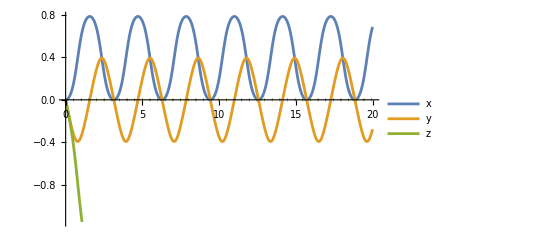

```mathematica
vars={u[1,t],u[2,t],u[3,t]};
j=3;

tf=20;
solj=NDSolve[wnEOMListi[[j]]/.θ->π/4,vars,{t,0,tf}]

ReImPlot[vars/.solj//Evaluate,{t,0,tf},PlotLegends->{"x", "y", "z"}]
```

### Check that all orderings give the same numerical solution

```mathematica
solList=Table[Flatten@NDSolve[wnEOMListi[[j]]/.θ->π/3,vars,{t,0,tf}],{j,1,3}]
```

{{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]},{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]},{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]}}

```mathematica
algebraMatList=Table[Permute[{({{0, 1}, {1, 0}}),({{0, -ⅈ}, {ⅈ, 0}}),({{1, 0}, {0, -1}})},perm],{perm,permutations}];
```

```mathematica
UtList=Table[MatrixExp[ⅈ u[1,t]algebraMatList[[j]][[1]]].MatrixExp[ⅈ u[2,t]algebraMatList[[j]][[2]]].MatrixExp[ⅈ u[3,t]algebraMatList[[j]][[3]]]/.solList[[j]],{j,1,3}];
```

```mathematica
UtList/.t->1.4
```

{{{0.169967+1.76838×10^-8 ⅈ,-0.492725-0.853424 ⅈ},{0.492725-0.853424 ⅈ,0.169967-1.76838×10^-8 ⅈ}},{{0.169967-6.35903×10^-8 ⅈ,-0.492725-0.853424 ⅈ},{0.492725-0.853424 ⅈ,0.169967+6.35903×10^-8 ⅈ}},{{0.169967+4.69438×10^-10 ⅈ,-0.492725-0.853424 ⅈ},{0.492725-0.853424 ⅈ,0.169967-4.69438×10^-10 ⅈ}}}

### Alternate algebra

```mathematica
co[OverHat[σz],(OverHat[σx]+ⅈ OverHat[σy])/2]//FullSimplify
co[OverHat[σz],(OverHat[σx]-ⅈ OverHat[σy])/2]//FullSimplify
co[(OverHat[σx]+ⅈ OverHat[σy])/2,(OverHat[σx]-ⅈ OverHat[σy])/2]//FullSimplify
```

OverHat[σx]+ⅈ OverHat[σy]

-OverHat[σx]+ⅈ OverHat[σy]

OverHat[σz]

```mathematica
Commutator[OverHat[σz],OverHat[σp],2 OverHat[σp]];
Commutator[OverHat[σz],OverHat[σm],-2 OverHat[σm]];
Commutator[OverHat[σp],OverHat[σm], OverHat[σz]];

algebra2={OverHat[σm],OverHat[σz],OverHat[σp]};

AlgCommTable[algebra2]
AlgCommTable[algebra2,Xj->True]
```

| OverHat[σm] | OverHat[σz] | OverHat[σp]
OverHat[σm] | 0 | 2 OverHat[σm] | -OverHat[σz]
OverHat[σz] | -2 OverHat[σm] | 0 | 2 OverHat[σp]
OverHat[σp] | OverHat[σz] | -2 OverHat[σp] | 0

| X_1 | X_2 | X_3
X_1 | 0 | 2 X_1 | -X_2
X_2 | -2 X_1 | 0 | 2 X_3
X_3 | X_2 | -2 X_3 | 0

```mathematica
OpSumListDecomposition[Total[algebra*hCoeffs]/.{OverHat[σx]->(OverHat[σp]+OverHat[σm]),OverHat[σy]->(OverHat[σp]-OverHat[σm])/ⅈ},algebra2]//FullSimplify
```

{{ⅈ Cos[θ]+Sin[θ],1},{-ⅈ Cos[θ]+Sin[θ],3}}

```mathematica
(*hCoeffs2={ⅈ ⅇ^(-ⅈ θ),0,-ⅈ ⅇ^(ⅈ θ)};*)
hCoeffs2={ⅈ Cos[θ]+Sin[θ],0,-ⅈ Cos[θ]+Sin[θ]};
Print["Hamilton: ",Ham2=Total@Flatten@Thread@{hCoeffs2*algebra2}];
```

Hamilton: OverHat[σp] (-ⅈ Cos[θ]+Sin[θ])+OverHat[σm] (ⅈ Cos[θ]+Sin[θ])

```mathematica
Ham2/.{OverHat[σp]->(OverHat[σx]+ⅈ OverHat[σy])/2,OverHat[σm]->(OverHat[σx]-ⅈ OverHat[σy])/2}//FullSimplify
```

Cos[θ] OverHat[σy]+OverHat[σx] Sin[θ]

```mathematica
{ut2,eom2}=MakeLieEOM[hCoeffs2,algebra2,algebra2]//FullSimplify;
sol2=Flatten@DSolve[Flatten@eom2,Flatten@ut2,t]//FullSimplify
```

{u[1,1,t]→Cos[t]^2,u[2,1,t]→-2 ⅇ^(-ⅈ θ) Cos[t] Sin[t],u[3,1,t]→-ⅇ^(-2 ⅈ θ) Sin[t]^2,u[1,2,t]→ⅇ^(ⅈ θ) Cos[t] Sin[t],u[2,2,t]→Cos[2 t],u[3,2,t]→ⅇ^(-ⅈ θ) Cos[t] Sin[t],u[1,3,t]→-ⅇ^(2 ⅈ θ) Sin[t]^2,u[2,3,t]→-2 ⅇ^(ⅈ θ) Cos[t] Sin[t],u[3,3,t]→Cos[t]^2}

```mathematica
σzpmt=Table[Sum[u[j,k,t]algebra2[[k]],{k,1,Length@algebra2}],{j,1,Length@algebra2}]/.sol2;
PrintσSol2[params_]:=(
Print["H = ",Ham2/.params];
(Print[#[[1]],"(t) = ",#[[2]]]&/@Thread[{algebra2,σzpmt/.params//FullSimplify}];)
);

PrintσSol2[{}]
```

H = OverHat[σp] (-ⅈ Cos[θ]+Sin[θ])+OverHat[σm] (ⅈ Cos[θ]+Sin[θ])

OverHat[σm](t) = Cos[t]^2 OverHat[σm]+ⅇ^(ⅈ θ) Sin[t] (Cos[t] OverHat[σz]-ⅇ^(ⅈ θ) OverHat[σp] Sin[t])

OverHat[σz](t) = Cos[2 t] OverHat[σz]-ⅇ^(-ⅈ θ) (OverHat[σm]+ⅇ^(2 ⅈ θ) OverHat[σp]) Sin[2 t]

OverHat[σp](t) = Cos[t]^2 OverHat[σp]+ⅇ^(-2 ⅈ θ) Sin[t] (ⅇ^(ⅈ θ) Cos[t] OverHat[σz]-OverHat[σm] Sin[t])

```mathematica
PrintσSol2[{θ->0}]
```

H = ⅈ OverHat[σm]-ⅈ OverHat[σp]

OverHat[σm](t) = Cos[t]^2 OverHat[σm]+Sin[t] (Cos[t] OverHat[σz]-OverHat[σp] Sin[t])

OverHat[σz](t) = Cos[2 t] OverHat[σz]-(OverHat[σm]+OverHat[σp]) Sin[2 t]

OverHat[σp](t) = Cos[t]^2 OverHat[σp]+Sin[t] (Cos[t] OverHat[σz]-OverHat[σm] Sin[t])

```mathematica
PrintσSol2[{θ->π/2}]
```

H = OverHat[σm]+OverHat[σp]

OverHat[σm](t) = Cos[t]^2 OverHat[σm]+Sin[t] (ⅈ Cos[t] OverHat[σz]+OverHat[σp] Sin[t])

OverHat[σz](t) = Cos[2 t] OverHat[σz]+ⅈ (OverHat[σm]-OverHat[σp]) Sin[2 t]

OverHat[σp](t) = Cos[t]^2 OverHat[σp]+Sin[t] (-ⅈ Cos[t] OverHat[σz]+OverHat[σm] Sin[t])

```mathematica
PrintσSol2[{θ->π/4}]
```

H = ((1+ⅈ) OverHat[σm])/(√2)+((1-ⅈ) OverHat[σp])/(√2)

OverHat[σm](t) = Cos[t]^2 OverHat[σm]+Sin[t] ((-1)^(1/4) Cos[t] OverHat[σz]-ⅈ OverHat[σp] Sin[t])

OverHat[σz](t) = Cos[2 t] OverHat[σz]+(-1)^(3/4) (OverHat[σm]+ⅈ OverHat[σp]) Sin[2 t]

OverHat[σp](t) = Cos[t]^2 OverHat[σp]+ⅈ Sin[t] (-(-1)^(1/4) Cos[t] OverHat[σz]+OverHat[σm] Sin[t])

```mathematica
weiCoeffs2=Table[a[j,t]->-ⅈ hCoeffs2[[j]],{j,1,3}];
ut2=Table[u[j,t],{j,1,3,1}];
wnEOM2=WeiNormanEOM[algebra2]/.weiCoeffs2
```

{u^(0,1)[1,t]==-ⅈ (ⅈ Cos[θ]+Sin[θ])+ⅈ (-ⅈ Cos[θ]+Sin[θ]) u[1,t]^2,u^(0,1)[2,t]==-ⅈ (-ⅈ Cos[θ]+Sin[θ]) u[1,t],u^(0,1)[3,t]==-ⅈ ⅇ^(-2 u[2,t]) (-ⅈ Cos[θ]+Sin[θ])}

```mathematica
algebra2
```

{OverHat[σm],OverHat[σz],OverHat[σp]}

```mathematica
wnEOM2i=wnEOM2/.{u[j_,t]:>ⅈ u[j,t],Derivative[0,1][u][j_,t]:>ⅈ Derivative[0,1][u][j,t]}//FullSimplify;
Print/@wnEOM2i;
```

ⅇ^(ⅈ θ) u[1,t]^2+ⅈ (Sin[θ]+u^(0,1)[1,t])==Cos[θ]

ⅇ^(ⅈ θ) u[1,t]+u^(0,1)[2,t]==0

ⅇ^(ⅈ θ)+ⅈ ⅇ^(2 ⅈ u[2,t]) u^(0,1)[3,t]==0

```mathematica
Print/@Table[First@Flatten@Solve[wnEOM2i[[j]], Derivative[0,1][u][j,t]]//TrigToExp//Simplify,{j,1,3}];
```

u^(0,1)[1,t]→ⅈ ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ) u[1,t]^2)

u^(0,1)[2,t]→-ⅇ^(ⅈ θ) u[1,t]

u^(0,1)[3,t]→ⅈ ⅇ^(ⅈ (θ-2 u[2,t]))

```mathematica
wnEOM2i
```

{ⅇ^(ⅈ θ) u[1,t]^2+ⅈ (Sin[θ]+u^(0,1)[1,t])==Cos[θ],ⅇ^(ⅈ θ) u[1,t]+u^(0,1)[2,t]==0,ⅇ^(ⅈ θ)+ⅈ ⅇ^(2 ⅈ u[2,t]) u^(0,1)[3,t]==0}

```mathematica
sol2=DSolve[wnEOM2i,{u[1,t],u[2,t],u[3,t]},t]//FullSimplify//Flatten
```

{u[1,t]→-ⅈ ⅇ^(-ⅈ θ) Tan[t-ⅈ C[1]],u[2,t]→C[2]-ⅈ Log[Cos[t-ⅈ C[1]]],u[3,t]→C[3]+ⅈ ⅇ^(ⅈ (θ-2 C[2])) Tan[t-ⅈ C[1]]}

```mathematica
sol2/.t->0
```

{u[1,0]→-ⅇ^(-ⅈ θ) Tanh[C[1]],u[2,0]→C[2]-ⅈ Log[Cosh[C[1]]],u[3,0]→C[3]+ⅇ^(ⅈ (θ-2 C[2])) Tanh[C[1]]}

```mathematica
sol2/.{C[1]->0,C[3]->0,C[2]->0}/.t->0
```

{u[1,0]→0,u[2,0]→0,u[3,0]→0}

```mathematica
sol2=sol2/.{C[1]->0,C[3]->0,C[2]->0}//FullSimplify
```

{u[1,t]→-ⅈ ⅇ^(-ⅈ θ) Tan[t],u[2,t]→-ⅈ Log[Cos[t]],u[3,t]→ⅈ ⅇ^(ⅈ θ) Tan[t]}

```mathematica
NDSolve[Join[wnIC,wnEOM2/.θ->0],{u[1,t],u[2,t],u[3,t]},{t,0,tf}]
```

NDSolve::ndsz: At t == 1.5708, step size is effectively zero; singularity or stiff system suspected.

{{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]}}

```mathematica
permutations={{1,2,3},{3,1,2},{2,3,1}};
algebraList=Table[Permute[algebra2,perm],{perm,permutations}]
weiCoeffsList=Table[Table[a[j,t]->-I  Permute[hCoeffs2,perm][[j]],{j,1,3}],{perm,permutations}]

wnEOMList=Table[Join[WeiNormanEOM[algebraList[[j]]]/.weiCoeffsList[[j]],wnIC],{j,1,Length@permutations}];
```

{{OverHat[σm],OverHat[σz],OverHat[σp]},{OverHat[σz],OverHat[σp],OverHat[σm]},{OverHat[σp],OverHat[σm],OverHat[σz]}}

{{a[1,t]→-ⅈ (ⅈ Cos[θ]+Sin[θ]),a[2,t]→0,a[3,t]→-ⅈ (-ⅈ Cos[θ]+Sin[θ])},{a[1,t]→0,a[2,t]→-ⅈ (-ⅈ Cos[θ]+Sin[θ]),a[3,t]→-ⅈ (ⅈ Cos[θ]+Sin[θ])},{a[1,t]→-ⅈ (-ⅈ Cos[θ]+Sin[θ]),a[2,t]→-ⅈ (ⅈ Cos[θ]+Sin[θ]),a[3,t]→0}}

```mathematica
vars={u[1,t],u[2,t],u[3,t]};
j=3;

tf=5;
solj=NDSolve[wnEOMList[[j]]/. θ->π/4,vars,{t,0,tf}]

(*ReImPlot[vars/. solj//Evaluate,{t,0,tf}]*)
```

NDSolve::ndsz: At t == 1.5708, step size is effectively zero; singularity or stiff system suspected.

{{u[1,t]→InterpolatingFunction[…][t],u[2,t]→InterpolatingFunction[…][t],u[3,t]→InterpolatingFunction[…][t]}}